#### In this document, we would like to verify whether the system controlling Acov(t) for the TurnOver model reaches equilibrium quickly or not. In order to do that, we need to look at (1) the solution to Acov’(t) containing only reactions that control its formation and (2) the solution to the Acov through the equilibrium constant expression.

```mathematica
ClearAll[mtot, ki, Atot, kj, A0]
```

Here, we try to solve for Acov(t) using the ODE for Acov through ki and kj processes:

```mathematica
FullSimplify[DSolve[{Acov'[t]==ki(mtot-Acov[t])(Atot-Acov[t]) - kj Acov[t], Acov[0]==A0},{Acov[t]},t]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Acov[t]→1/(2 ki)(kj+ki (Atot+mtot)+√(-Atot^2 ki^2+2 Atot ki (-kj+ki mtot)-(kj+ki mtot)^2) Tan[1/2 √(-(Atot ki+kj)^2+2 ki (Atot ki-kj) mtot-ki^2 mtot^2) t-ArcTan[(kj+ki (-2 A0+Atot+mtot))/(√(-Atot^2 ki^2+2 Atot ki (-kj+ki mtot)-(kj+ki mtot)^2))]])}}

Then, we solve the equilibrium expression for Acov:

```mathematica
FullSimplify[Solve[Acov kj== ki(mtot-Acov)(Atot-Acov),Acov]]
```

{{Acov→(Atot ki+kj+ki mtot-√(-4 Atot ki^2 mtot+(kj+ki (Atot+mtot))^2))/(2 ki)},{Acov→(Atot ki+kj+ki mtot+√(-4 Atot ki^2 mtot+(kj+ki (Atot+mtot))^2))/(2 ki)}}

To find the time that practically, the Acov(t) system reaches equilibrium i.e. t_c, we need to find t_c where Acov(t_c) == 0.95 Acov(t_equilibrium). Using manual manipulation (pen and paper), t_c was found to have an expression of such form:

```mathematica
const1 = kj + ki Atot + ki mtot;
const2 = -(Atot ki + kj)^2  + 2 ki (Atot ki - kj) mtot - ki^2  mtot^2;
const3 = kj + ki(-2A0 + Atot + mtot);
t_c = 2ArcTan[(0.95 Sqrt[-(const2^2)] - 0.05 const1 Sqrt[const2] + const3 Sqrt[const2])/(const2 + 0.95const3 Sqrt[-const2] + 0.05 const1 const3)]/Sqrt[const2]
```

(2 ArcTan[(-0.05 (Atot ki+kj+ki mtot) √(-(Atot ki+kj)^2+2 ki (Atot ki-kj) mtot-ki^2 mtot^2)+0.95 √(-(-(Atot ki+kj)^2+2 ki (Atot ki-kj) mtot-ki^2 mtot^2)^2)+√(-(Atot ki+kj)^2+2 ki (Atot ki-kj) mtot-ki^2 mtot^2) (kj+ki (-2 A0+Atot+mtot)))/(-(Atot ki+kj)^2+2 ki (Atot ki-kj) mtot-ki^2 mtot^2+0.05 (Atot ki+kj+ki mtot) (kj+ki (-2 A0+Atot+mtot))+0.95 √((Atot ki+kj)^2-2 ki (Atot ki-kj) mtot+ki^2 mtot^2) (kj+ki (-2 A0+Atot+mtot)))])/(√(-(Atot ki+kj)^2+2 ki (Atot ki-kj) mtot-ki^2 mtot^2))

Let’s assign the optimised values for the kinetic parameters from the turnover.py program fittings, and then proceed to solve for the time taken to reach 95% equilibrium state:

```mathematica
ki = 3118206;
kj = 0.1;
Atot = 10^-7;
A0 = 0;
mtot = 9.6*10^-6;
t_c = 2ArcTan[(0.95 Sqrt[-(const2^2)] - 0.05 const1 Sqrt[const2] + const3 Sqrt[const2])/(const2 + 0.95const3 Sqrt[-const2] + 0.05 const1 const3)]/Sqrt[const2]
```

0.00077024-0.105688 ⅈ

### WHAAAAAT? Apparently, it’s imaginary ...

Just plotting the solution to the Acov’(t) shows:

```mathematica
AcovSol[ki_,kj_,Atot_, mtot_, t_, A0_]:=1/(2 ki)(kj+ki (Atot+mtot)+√(-Atot^2 ki^2+2 Atot ki (-kj+ki mtot)-(kj+ki mtot)^2) Tan[1/2 √(-(Atot ki+kj)^2+2 ki (Atot ki-kj) mtot-ki^2 mtot^2) t-ArcTan[(kj+ki (-2 A0+Atot+mtot))/(√(-Atot^2 ki^2+2 Atot ki (-kj+ki mtot)-(kj+ki mtot)^2))]])
```

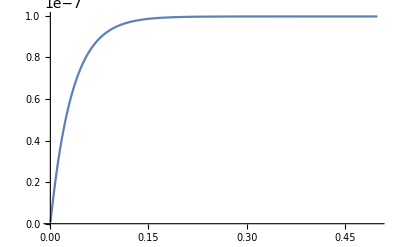

```mathematica
Plot[AcovSol[ki,kj,Atot,Const,t,A0],{t,0,0.5},PlotRange->All]
```

So it seems that compared to the magnitude of the total time of reaction, the time taken to reach equilibrium is quite small. 
This means that it would be largely reasonable to assume the presence of an equilibrium in Acov formation from m(t) and A_free(t) upon the introduction of efforts to add complexities to the TurnOver model. 

This conclusion is also qualitatively supported by the analysis of the mechanisms controlling the flux of A_cov(t). The fluxes based on the numerical evaluation of the ODEs with the fitted parameters (to the steady-state solution) suggest that the rates of mechanisms concerning surface coverage by monomers AND replacement of the surface to become free due to fibril formation reach equality pretty quickly. Hence, an equilibrium can be assumed.  

-Graphics-
Image generated from Python code evaluating the fluxes.
*kinks towards the end could be due to sensitivity errors associated with numerical solving of ODEs due to the use of very small unites, of 10^-6 orders.